# Evolutionary Dynamics Ch.2

## 2.1 Reproduction

exponential growth difference equation

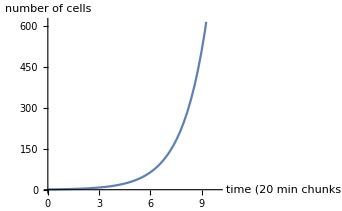

```mathematica
Plot[1*2^t,{t,0,10},AxesLabel->{"time (20 min chunks)","number of cells"}]
```

differential equation version of exponential difference equation. 5/36 is because ten 20 minute chunks is 5/36 of a day. rate of 72 means that there are an average of 72 cell divisions in a day, ie; 1440/x=20 and  then x=72

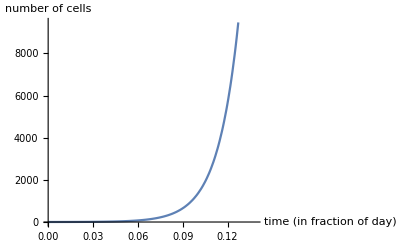

```mathematica
Plot[1*ⅇ^(72 t),{t,0,5/36},AxesLabel->{"time (in fraction of day)","number of cells"}]
```

Deterministic Chaos: 2.1.1

```mathematica
logGrowth[x0_,r_,k_,t_]:=(k*x0*ⅇ^(r*t))/(k+x0*(ⅇ^(r*t)-1));
```

```mathematica
logDiff[a_,x_]:=a*x*(1-x);
```

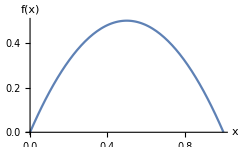

```mathematica
Plot[logDiff[#,x]&@2,{x,0,1},AxesLabel->{"x","f(x)"}]
```

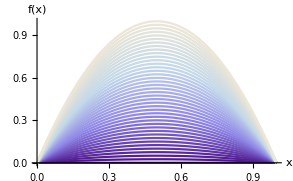

```mathematica
Plot[Evaluate[Table[logDiff[a,x],{a,0,4,0.1}]],{x,0,1},AxesLabel->{"x","f(x)"},PlotStyle->Table[ColorData["LakeColors"][x],{x,0,1,1/41}]]
```

## 2.2 Selection

2.2.2 Survival of the first, survival of all
Note that the vector field shows that even when one fitness value is less than the other, when c<1 we still see coexistence of both species (sub-exponential growth). When c>1 we do not see this and there is always a fixation of one species if fitness values not equal There is only coexistence when fitness values and population sizes are exactly the same. When c=0 the growth rate only depends on a and b, so there is always coexistence (immigration from somewhere else parameterized by a & b).
Takeaway: c<1: survival of all, c>1: survival of first

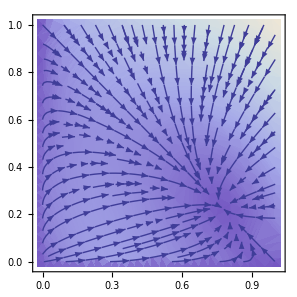

```mathematica
StreamDensityPlot[
{
a x^c-(a x^c+b y^c) x,
b y^c-(a x^c+b y^c) y
}/.{a->.65,b->.35,c->0.5},
{x,0,1},{y,0,1},StreamScale->Automatic,StreamPoints->Automatic,PlotTheme->"Classic"
]
```

## 2.3 Mutation

Errors of copying genetic code in reproduction = mutation. 
ODEs: mu1 is A->B mutation; mu2 is inverse.

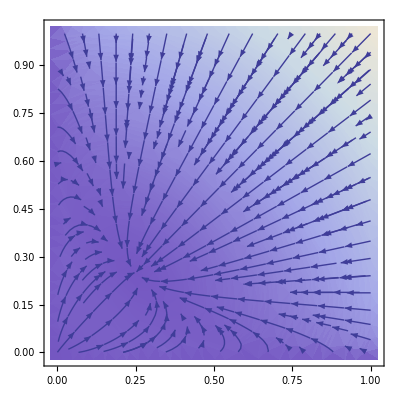

```mathematica
StreamDensityPlot[
{
x (1-Subscript[μ, 1])+y Subscript[μ, 2]- (a x^c+b y^c) x,
x Subscript[μ, 1]+y (1-Subscript[μ, 2])-(a x^c+b y^c) y
}/.{a->1,b->1,c->0.5,Subscript[μ, 1]-> 0.95,Subscript[μ, 2]-> 0.9},
{x,0,1},{y,0,1},StreamScale->Automatic,StreamPoints->Automatic,PlotTheme->"Classic"
]
```

2.3.1 Mutation Matrix:
Extend mutation dynamics to n different species. Just a transition matrix; globally stable equilibrium population size of the n species is just the left-hand eigenvector associated with the eigenvalue = 1.

2.4 Mating:
3 genotype, p, q are allele frequency.

```mathematica
mateDyn[1][x_,y_]:=x+1/2 y
mateDyn[2][y_,z_]:=z+1/2 y
mateDyn[3][p_]:=p^2
mateDyn[4][p_,q_]:=2 p q
mateDyn[5][q_]:=q^2
```